```mathematica
(*Sergio Villamarin*)
(*solutions plots section*)
ClearAll[x0,h,x,t,x0s]
roots = Solve[0==x(1-x)-h,{x}]
rvalues = roots/.h->0.3
```

{{x→1/2 (1-√(1-4 h))},{x→1/2 (1+√(1-4 h))}}

{{x→0.5-0.223607 ⅈ},{x→0.5+0.223607 ⅈ}}

```mathematica
ClearAll[x0,h,x,t,x0s]
x0s={0.02, 0.05, 0.1, 0.2,0.23, 0.27, 0.3, 0.4, 0.5,0.6, 0.8};
tabla = Table[
With[{h=0.3, x0=x0s[[i]]},
Evaluate[NDSolve[{x'[t]==x[t](1-x[t])-h, x[0]==x0, WhenEvent[x[t]==0, x[t]->0.001]},x[t],{t, 0,10}]]
],{i,Length[x0s]} ]
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

General::stop: Further output of NDSolve::ndinnt will be suppressed during this calculation.

{{{x[t]→InterpolatingFunction[…][t]}},{{x[t]→InterpolatingFunction[…][t]}},{{x[t]→InterpolatingFunction[…][t]}},{{x[t]→InterpolatingFunction[…][t]}},{{x[t]→InterpolatingFunction[…][t]}},{{x[t]→InterpolatingFunction[…][t]}},{{x[t]→InterpolatingFunction[…][t]}},{{x[t]→InterpolatingFunction[…][t]}},{{x[t]→InterpolatingFunction[…][t]}},{{x[t]→InterpolatingFunction[…][t]}},{{x[t]→InterpolatingFunction[…][t]}}}

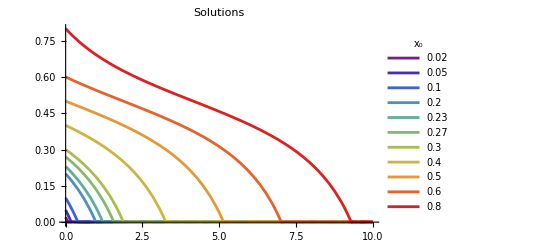

```mathematica
g1= Plot[Evaluate[x[t]/.tabla],{t,0,10}, Evaluated->True,
PlotLegends->LineLegend[x0s,LegendLabel->Subscript[x, 0]],
PlotLabel->HoldForm[Solutions], PlotStyle->"Rainbow",
GridLines->{{}, {}},GridLinesStyle->{{Black,,Thickness[0.005]},None}]
```

```mathematica
(*Potential plots section*)
```

```mathematica
V[x_]:=h*x-x^2/2+x^3/3
```

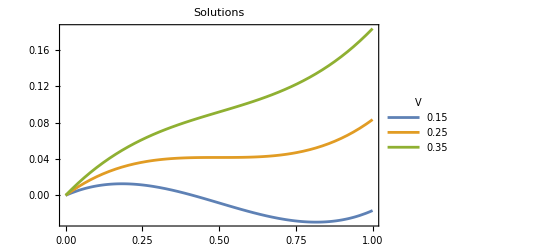

```mathematica
Plot[Evaluate[Table[V[x],{h,{0.15,0.25,0.35}}]],{x,0,1}, Frame->True,
PlotLegends->LineLegend[Table[h,{h,{0.15,0.25,0.35}}],LegendLabel->V],
PlotLabel->HoldForm[Solutions],LabelStyle->{GrayLevel[0]}]
```